```mathematica
(*Se inicializa el paquete que permite correr comandos de R dentro de Mathematica*)
Needs["RLink`"]
InstallR[]
```

```mathematica
(*Se lee la tabla mediante un comando de R y se transforma a formato de Mathematica como el objeto data*)
REvaluate["load('/Users/nicolas/Documents/school/Actuarial/tabla1.Rdata')"];
data=RGetData[REvaluate["tabla1"]];
```

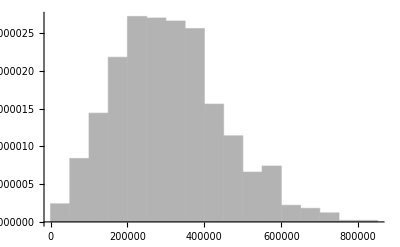

```mathematica
(*Se realiza una simulación de 1000 valores de S y se hace un histograma para entender su distribución*)
SeedRandom[137];
sim=Transpose[Table[RandomVariate[BernoulliDistribution[p],1000],{p,data[[3]]}]].data[[2]];
hist=Histogram[sim,{50000},"PDF",PlotTheme->"Monochrome"]
```

```mathematica
(*Se estiman los parámetros para las 4 distribuciones por el método de los momentos, en el caso de la Weibull es solo una aproximación mediante minimización*)
{{θnorm},{θlogn},{θgam}}=Table[Solve[{Moment[dist[θ1,θ2],1]==data[[3]].data[[2]],CentralMoment[dist[θ1,θ2],2]==(data[[3]](Table[1,1000]-data[[3]])).data[[2]]^2},{θ1,θ2},PositiveReals],{dist,{NormalDistribution,LogNormalDistribution,GammaDistribution}}];
θweib=Minimize[{Abs[(Mean[WeibullDistribution[θ1,θ2]]-data[[3]].data[[2]])(StandardDeviation[WeibullDistribution[θ1,θ2]]-√((data[[3]](Table[1,1000]-data[[3]])).data[[2]]^2))],θ2>data[[3]].data[[2]]},{θ1,θ2}][[2]];
θweib[[2]]=θ2->(data[[2]].data[[3]])/Gamma[1+1/θ1]/.θweib[[1]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Se crean las cuatro distribuciones con parámetros estimados*)
norm=NormalDistribution[θ1,θ2]/.θnorm;
logn=LogNormalDistribution[θ1,θ2]/.θlogn;
gam=GammaDistribution[θ1,θ2]/.θgam;
weib=WeibullDistribution[θ1,θ2]/.θweib;
dists={norm,logn,gam,weib};
names={"Normal","Log-Normal","Gamma","Weibull"};
```

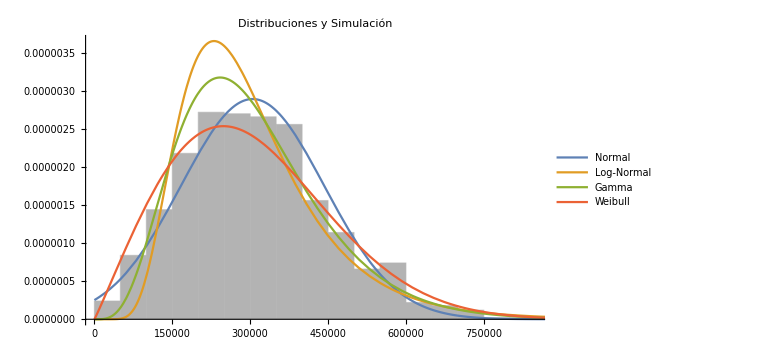

```mathematica
(*Se miran las densidades de las 4 distribuciones sobre el histograma hecho anteriormente como guía*)
pdfs=Table[PDF[dist,x],{dist,dists}];
plots=Plot[pdfs,{x,0,1000000},PlotLegends->names];
Show[hist,plots,PlotLabel->"Distribuciones y Simulación",ImageSize->Large,LabelStyle->Directive[FontSize->14]]
```

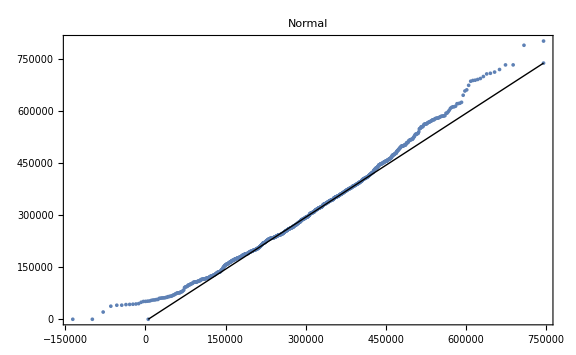
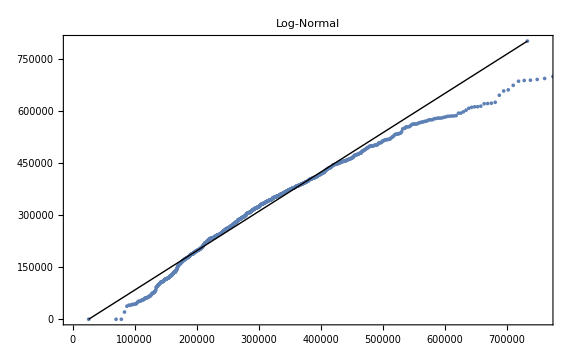
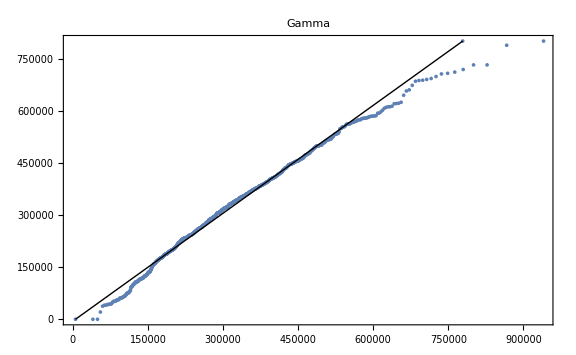
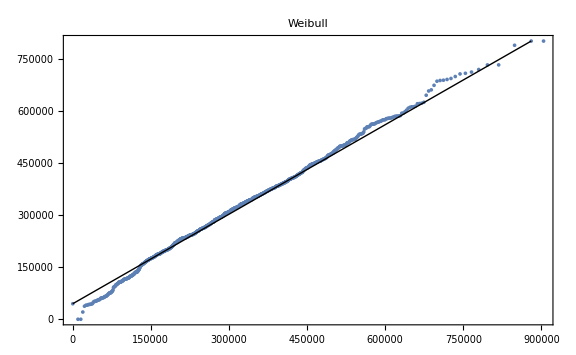

```mathematica
(*Se realizan los 4 Q-Q plots comparándo cuantiles simulados contra cuantiles de las distribuciones*)
Table[QuantilePlot[sim,dists[[i]],PlotLabel->names[[i]],ImageSize->Large,LabelStyle->Directive[FontSize->14]],{i,4}]
```

```mathematica
(*Se genera una tabla de resultados del test de Cramér-von Mises para cada distribución, se dan p-valores y conclusión*)
{names,Table[CramerVonMisesTest[sim,dist],{dist,dists}],Table[CramerVonMisesTest[sim,dist,"ShortTestConclusion"],{dist,dists}]}//TableForm
```

Normal | Log-Normal | Gamma | Weibull
0.234443 | 0.0000221153 | 0.0118911 | 0.
Do not reject | Reject | Reject | Reject

```mathematica
(*Se realizan 1000 simulaciones de 1000 realizaciones de S para el test χ^2 y se calculan los primeros 5 momentos empíricos para cada una*)
sims=Table[Transpose[Table[RandomVariate[BernoulliDistribution[p],1000],{p,data[[3]]}]].data[[2]],1000];
μemps=Table[Table[Moment[sims[[i]],r],{r,1,5}],{i,1,1000}];
```

```mathematica
(*Se calculan los 10 primeros momentos para cada distribución y las 4 matrices de covarianza correspondientes, todo esto de manera simbólica*)
μnorm=Table[Moment[NormalDistribution[θ1,θ2],r],{r,1,10}];
μlogn=Table[Moment[LogNormalDistribution[θ1,θ2],r],{r,1,10}];
μgam=Table[Moment[GammaDistribution[θ1,θ2],r],{r,1,10}];
μweib=Table[Moment[WeibullDistribution[θ1,θ2],r],{r,1,10}];
{Cnorm,Clogn,Cgam,Cweib}=Table[Inverse[({{μ[[6]]-μ[[3]]^2, μ[[7]]-μ[[3]]μ[[4]], μ[[8]]-μ[[3]]μ[[5]]}, {μ[[7]]-μ[[3]]μ[[4]], μ[[8]]-μ[[4]]^2, μ[[9]]-μ[[4]]μ[[5]]}, {μ[[8]]-μ[[3]]μ[[5]], μ[[9]]-μ[[4]]μ[[5]], μ[[10]]-μ[[5]]^2}})],{μ,{μnorm,μlogn,μgam,μweib}}];
```

```mathematica
(*Se definen las 4 funciones que arrojarán el valor del estadístico dados momentos empíricos y parámetros para la distribución apropiada*)
fnorm[μemp_,θ_]:=fnorm[μemp,θ]=(
νnorm=√1000{μemp[[3]],μemp[[4]],μemp[[5]]}-({μnorm[[3]],μnorm[[4]],μnorm[[5]]}/.θ);
Transpose[νnorm].(Cnorm/.θ).νnorm)
flogn[μemp_,θ_]:=flogn[μemp,θ]=(
νlogn=√1000{μemp[[3]],μemp[[4]],μemp[[5]]}-({μlogn[[3]],μlogn[[4]],μlogn[[5]]}/.θ);
Transpose[νlogn].(Clogn/.θ).νlogn)
fgam[μemp_,θ_]:=fgam[μemp,θ]=(
νgam=√1000{μemp[[3]],μemp[[4]],μemp[[5]]}-({μgam[[3]],μgam[[4]],μgam[[5]]}/.θ);
Transpose[νgam].(Cgam/.θ).νgam)
fweib[μemp_,θ_]:=fweib[μemp,θ]=(
νweib=√1000{μemp[[3]],μemp[[4]],μemp[[5]]}-({μweib[[3]],μweib[[4]],μweib[[5]]}/.θ);
Transpose[νweib].(Cweib/.θ).νweib)
```

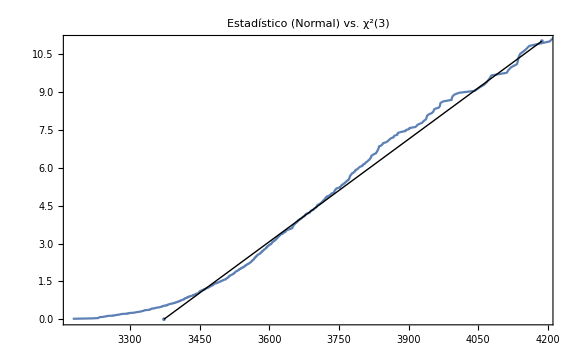
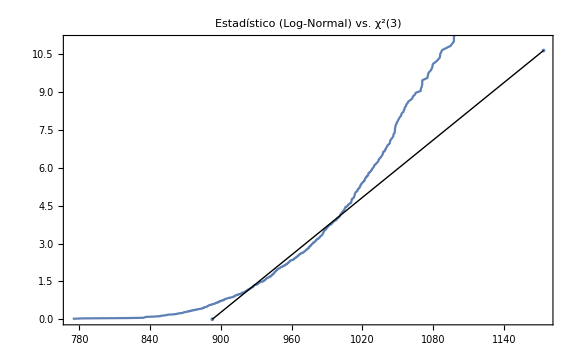
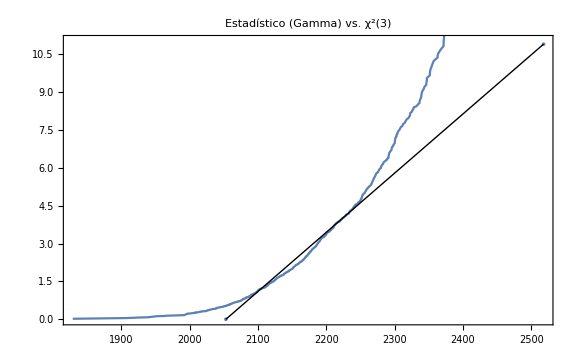
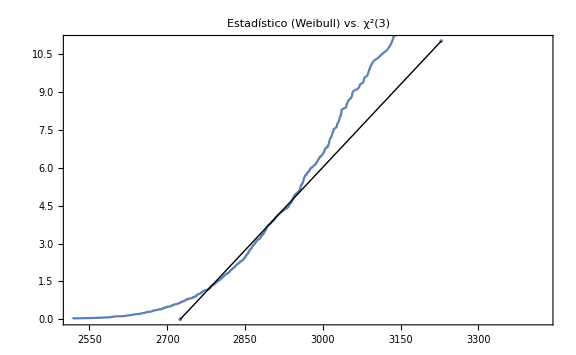

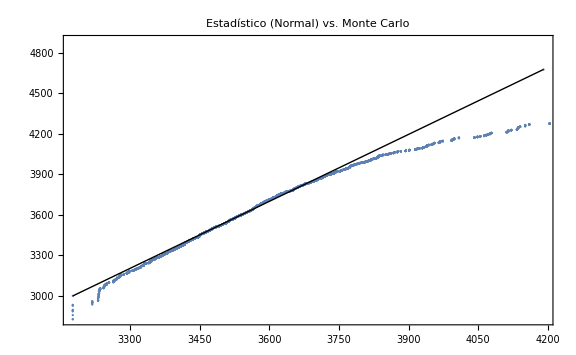
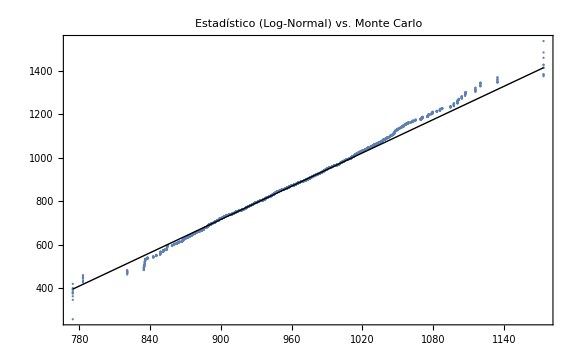
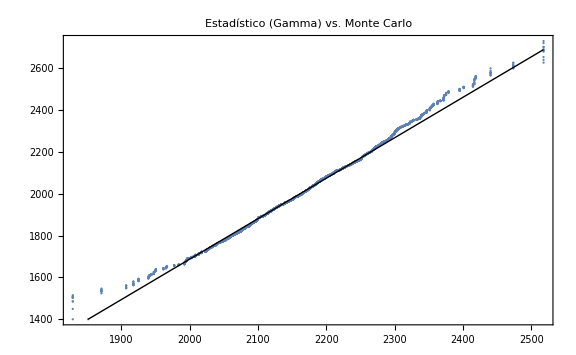
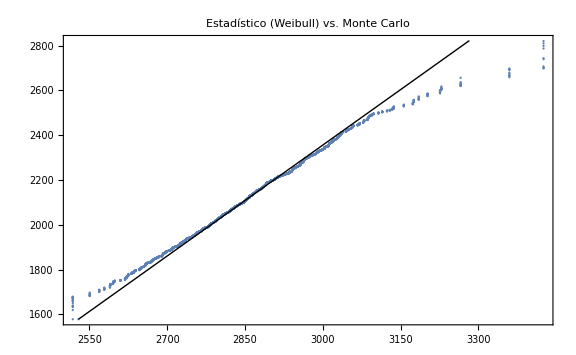

```mathematica
(*Se calcúlan los 1000 valores del estadístico para las 1000 simulaciones, luego se simulan 10000 veces 1000 realizaciones de la distribución estimada y se calculan los valores del estadístico, finalmente se generan los Q-Q plots comparando cuantiles del estadístico a partit de las empíricas con cuantiles χ^2(3) y con cuantiles Monte Carlo*)
χ={Table[fnorm[μemps[[i]],θnorm],{i,1,1000}],Table[flogn[μemps[[i]],θlogn],{i,1,1000}],Table[fgam[μemps[[i]],θgam],{i,1,1000}],Table[fweib[μemps[[i]],θweib],{i,1,1000}]};
Snorm=Table[RandomVariate[norm,1000],10000];
μempsnorm=Table[Table[Moment[Snorm[[i]],r],{r,1,10}],{i,1,10000}];
χnormn=Table[θnormn=FindDistributionParameters[Snorm[[i]],NormalDistribution[θ1,θ2],ParameterEstimator->"MethodOfCentralMoments"];fnorm[μempsnorm[[i]],θnormn],{i,1,10000}];
Slogn=Table[RandomVariate[logn,1000],10000];
μempslogn=Table[Table[Moment[Slogn[[i]],r],{r,1,10}],{i,1,10000}];
χlognn=Table[θlognn=FindDistributionParameters[Slogn[[i]],LogNormalDistribution[θ1,θ2],ParameterEstimator->"MethodOfCentralMoments"];flogn[μempslogn[[i]],θlognn],{i,1,10000}];
Sgam=Table[RandomVariate[gam,1000],10000];
μempsgam=Table[Table[Moment[Sgam[[i]],r],{r,1,10}],{i,1,10000}];
χgamn=Table[θgamn=FindDistributionParameters[Sgam[[i]],GammaDistribution[θ1,θ2],ParameterEstimator->"MethodOfCentralMoments"];fgam[μempsgam[[i]],θgamn],{i,1,10000}];
Sweib=Table[RandomVariate[weib,1000],10000];
μempsweib=Table[Table[Moment[Sweib[[i]],r],{r,1,10}],{i,1,10000}];
χweibn=Table[θweibn=FindDistributionParameters[Sweib[[i]],WeibullDistribution[θ1,θ2],ParameterEstimator->"MethodOfCentralMoments"];fweib[μempsweib[[i]],θweibn],{i,1,10000}];
χn={χnormn,χlognn,χgamn,χweibn};
Table[QuantilePlot[ChiSquareDistribution[3],χ[[i]],PlotLabel->"Estadístico ("<>names[[i]]<>") vs. χ^2(3)",ImageSize->Large,LabelStyle->Directive[FontSize->14]],{i,1,4}]
Table[QuantilePlot[χn[[i]],χ[[i]],PlotLabel->"Estadístico ("<>names[[i]]<>") vs. Monte Carlo",ImageSize->Large,LabelStyle->Directive[FontSize->14]],{i,1,4}]
```

```mathematica
(*Se discretizan la variable de severidad y se construye su distribución*)
dataD=Ceiling[data[[2]],1000];
fZ=PDF[EmpiricalDistribution[dataD],z];
```

```mathematica
(*Se define el parámetro Poisson como la suma de las probabilidades de muerte y se construye la distribución de S mediante recursión*)
λ=Total[data[[3]]];
fS={ⅇ^-λ};
For[w=1,w≤900,w++,AppendTo[fS,λ/w∑_(y=1)^Min[w,84] y (fX/.{z->y 1000})fS[[w-y+1]]]];
```

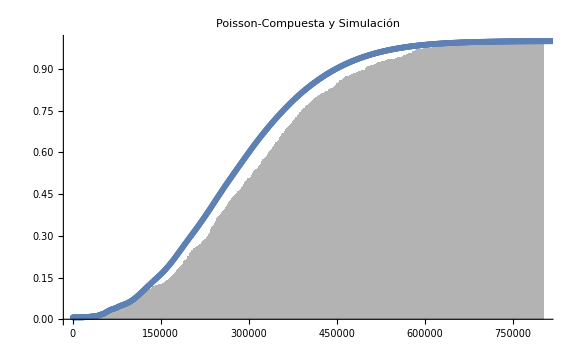

```mathematica
(*Se define la distribución acumulada de S y se compara con la simulación*)
FS=Table[Total[fS[[1;;i]]],{i,1,Length[fS]}];
distD=Transpose[{Table[i 1000,{i,0,900}],FS}];
Show[Histogram[sim,{1000},"CDF",PlotTheme->"Monochrome"],ListPlot[distD],PlotLabel->"Poisson-Compuesta y Simulación",ImageSize->Large,LabelStyle->Directive[FontSize->14]]
```

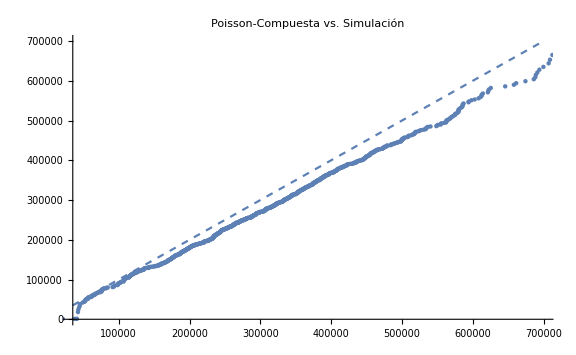

```mathematica
(*Se construyen los cuantiles y se genera el Q-Q plot comparando la distribución Poisson compuesta vs. la simulación*)
qq=Table[{Quantile[sim,q],FirstPosition[FS,_?(#>q&)][[1]]1000},{q,0.001,0.999,0.001}];
Show[Plot[x,{x,35000,700000},PlotStyle->Dashed],ListPlot[qq],PlotLabel->"Poisson-Compuesta vs. Simulación",ImageSize->Large,LabelStyle->Directive[FontSize->14]]
```